```mathematica
NotebookEvaluate[NotebookDirectory[]<>"../setup.nb"]
```

```mathematica
abortOnMessageOn[]
```

### Segmentation data (mesh) loading and pre-processing

#### Mesh export/import setup

```mathematica
exportTimeseriesHDF5[file_,data_]:=With[{numDigits=Ceiling[Log10[Length[data]]]},
Export[file,Table["TP"<>IntegerString[t,10,numDigits]->data[[t]],{t,Length[data]}],"Datasets"]
];
```

```mathematica
padRaggedArray[array_,pad_:0]:=With[{maxLength=Max[Length/@array]},PadRight[#,maxLength,pad]&/@array]
```

```mathematica
flattenAssociation[assoc_]:=Flatten/@List@@@Normal[assoc]
```

```mathematica
ClearAll[removePadding];
removePadding[list:{_Integer..},pad_:0]:=With[{
pos=FirstPosition[Reverse[list],Except[pad],1,Heads->False]
},
If[pos==={},(* everything is padding *)
{},
list[[1;;-First[pos]]]
]
];
removePadding[array_,pad_:0]/;Depth[array]>=3:=removePadding[#,pad]&/@array;
```

```mathematica
toAssoc[data:{{__}..}]:=Association[First[#]->Rest[#]&/@data];
```

```mathematica
importHDF5Timeseries[file_]:=With[{data=Import[file,"Data"]},
Values[KeySort[data]]
]
```

#### Load mesh data from h5 files

```mathematica
baseDir=NotebookDirectory[]<>"../../Data/Snail/Snapshot Meshes/";
```

Check that the files are there

```mathematica
FileNames[baseDir<>"*.h5"]//Length
```

7

Load the timeseries data. Note that the cell ids are not consistent across timepoints. For tracked cells, see “Tracked Meshes” directory

```mathematica
cellVerticesTS=EchoTiming[toAssoc/@removePadding[importHDF5Timeseries[baseDir<>"cellVertices.h5"]]];
cellNeighborsTS=EchoTiming[toAssoc/@removePadding[importHDF5Timeseries[baseDir<>"cellNeighbors.h5"]]];
cellCentroidsTS=EchoTiming[toAssoc/@importHDF5Timeseries[baseDir<>"cellCentroids.h5"]];
vertexCoordsTS=EchoTiming[importHDF5Timeseries[baseDir<>"vertexCoords.h5"]];
vertex2DCoordsTS=EchoTiming[importHDF5Timeseries[baseDir<>"vertexCoords2D.h5"]];
vertexCellsTS=EchoTiming[removePadding[importHDF5Timeseries[baseDir<>"vertexCells.h5"]]];
vertexCellsTS=EchoTiming[removePadding[importHDF5Timeseries[baseDir<>"vertexNeighbors.h5"]]];
```

3.27965

3.1279

0.387509

0.070425

0.082178

4.04

4.39924

#### Setup cylinder projection parameters

```mathematica
$axisOffset=Mean[cellCentroidsTS[[1]]];
boundingBox=MinMax/@Transpose[Values[cellCentroidsTS[[1]]]];
$radius=Mean[Join[Abs[boundingBox[[2]]-$axisOffset[[2]]],Abs[boundingBox[[3]]-$axisOffset[[3]]]]];
```

```mathematica
$majorHalfAxis=230
```

230

```mathematica
Graphics3D[{
FaceForm[None],
(*GraphicsComplex[vertexCoordsTS[[1]],Polygon/@Take[Values[cellVerticesTS[[1]]]]],*)
Point[meshTS[[1]]["VertexCoords3D"]],
FaceForm[Opacity[0.5]],Ellipsoid[{0,0,0},{$majorHalfAxis,$radius,$radius}]
},
Boxed->False
]
```

-Graphics3D-

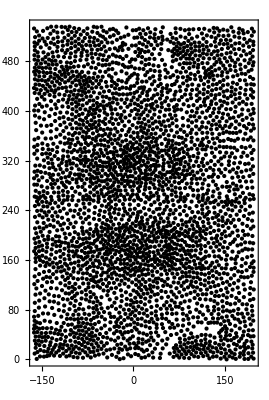

```mathematica
Graphics[{
Point[toCylinder[#]]&/@Values[cellCentroidsTS[[-1]]]
},
Frame->True
]
```

#### Identify excessively large cells that are likely segmentation erros

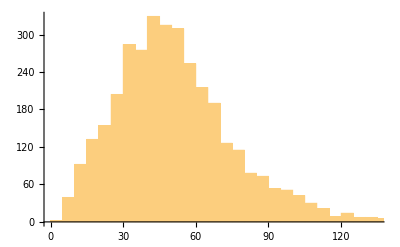

```mathematica
Histogram[Table[cellArea[c,60],{c,Length[cellCentroidsTS[[60]]]}]]
```

```mathematica
largeCells=Select[Range[Length[cellCentroidsTS[[25]]]],cellArea[#,25]>150&];
```

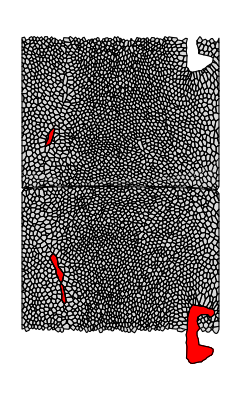

```mathematica
Graphics[{
FaceForm[LightGray],EdgeForm[Black],renderCell2D[#,25]&/@Range[Length[cellCentroidsTS[[25]]]],
FaceForm[Red],renderCell2D[#,25]&/@largeCells
}]
```

```mathematica
excludedCellsTS=Table[Select[Range[Length[cellCentroidsTS[[t]]]],cellArea[#,t]>150&],{t,Length[cellCentroidsTS]}];//AbsoluteTiming
```

{31.7999,Null}

```mathematica
Length/@excludedCellsTS
```

{0,0,0,0,0,0,0,0,0,1,1,1,1,1,1,1,2,2,1,4,5,4,5,5,4,7,8,9,9,8,6,6,8,7,6,11,8,12,8,6,9,6,7,9,12,5,8,7,11,9,9,9,10,11,17,10,14,17,14,14}

### Analysis

#### Isogonal strain

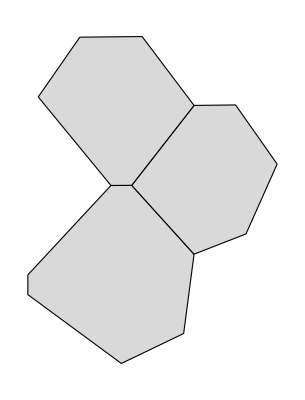

```mathematica
Graphics[{FaceForm[LightGray],EdgeForm[Black],renderCell2D[#,1]&/@vertexCellsTS[[1]][[1000]]},ImageSize->Tiny]
```

```mathematica
vertexIsogonalStrain[1000,1,4.2]
```

{{0.991814,0.0276887},{0.0276887,1.16573}}

Crop vertices at the edge of the pullback where cells are cropped.

```mathematica
selectionBox={{20,1000},{20,680}};
```

```mathematica
nonBoundaryVertices[box_,t_]:=First/@Position[vertex2DCoordsTS[[t]],_?(inBoxQ[#,box]&),{1},Heads->False];
```

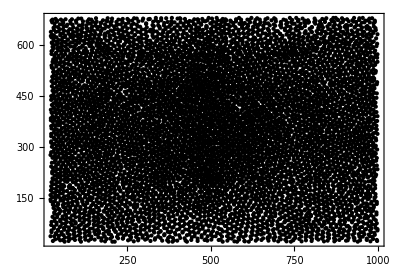

```mathematica
With[{vertices=nonBoundaryVertices[selectionBox,1]},
Graphics[Point[vertex2DCoordsTS[[1,vertices]]],Frame->True]
]
```

```mathematica
Block[{t=20,scaleFactor=4.2,selectedVertices},
(* crop pullback edges *)
selectedVertices=nonBoundaryVertices[selectionBox,t];
Echo[Length[selectedVertices]];
(* select one half of the embryo *)
selectedVertices=Select[selectedVertices,vertexCoordsTS[[t,#,3]]>$axisOffset[[3]]&];
Echo[Length[selectedVertices]];
(* excluded degenerate vertices (more or less than three cells meeting) *)
selectedVertices=Select[selectedVertices,Length[vertexCellsTS[[t,#]]]==3&];

Echo[Length[selectedVertices]];
vertexData=
DeleteCases[
{toCylinder[vertexCoordsTS[[t,#]]],vertexIsogonalStrain[#,t,scaleFactor]}&/@selectedVertices,
{_,_Missing}
];//AbsoluteTiming
]
```

7901

4154

4138

{2.24023,Null}

```mathematica
magenta=RGBColor[0.9,0.3,0.8];
```

```mathematica
renderTensor[p_,S_,scale_:1]:=With[{es=Eigensystem[(S+Transpose[S])/2]},{
If[es[[1,1]]<0,magenta,Darker[Cyan]],
Line[{p-#,p+#}&@(scale es[[1,1]]es[[2,1]])],
If[es[[1,2]]<0,magenta,Darker[Cyan]],
Line[{p-#,p+#}&@(scale es[[1,2]]es[[2,2]])]
}]
```

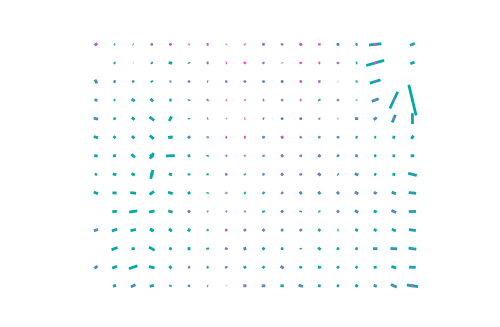

```mathematica
With[{
binnedData=Mean[#[[All,2]]]&/@Select[GroupBy[vertexData,{0,-10}+Round[{0,10}+#[[1]],20]&],Length[#]>2&]
},Graphics[{
AbsolutePointSize[5],AbsoluteThickness[2],
FaceForm[LightGray],EdgeForm[LightGray],
EdgeForm[{Dashed,AbsoluteThickness[1],Black}],FaceForm[None],
KeyValueMap[Function[{c,tensor},
renderTensor[c,tensor-IdentityMatrix[2],5]
],
binnedData
]},
Frame->False,
PlotRange->{{-164-50,200+25},{π,2π}$radius+{-10,10}},
ImageSize->500,Background->White
]
]
```

Cell array plot to localize CF and PMG.

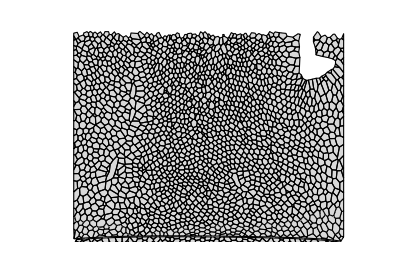

```mathematica
Graphics[{
FaceForm[LightGray],EdgeForm[Black],renderCell2D[#,25]&/@Range[Length[cellCentroidsTS[[25]]]]
},
PlotRange->{{-164-50,200+25},{π,2π}$radius+{-10,10}}
]
```

#### Isogonal strain in ventral ectoderm

```mathematica
Graphics[{
FaceForm[LightGray],EdgeForm[Black],renderCell2D[#,25]&/@Range[Length[cellCentroidsTS[[25]]]],
FaceForm[None],EdgeForm[{Red,AbsoluteThickness[2]}],
Rectangle[{-100,π $radius},{180,π $radius+60}]
},
PlotRange->{{-164-50,200+25},{π,2π}$radius+{-10,10}}
]
```

```mathematica
selectedVertices=Select[Range[Length[vertexCoordsTS[[1]]]],inBoxQ[toCylinder[vertexCoordsTS[[1,#]]],{{-100,180},π $radius+{0,60}}]&];
```

```mathematica
vertexDataTS=Block[{scaleFactor=4.2,selectedVertices},
Table[selectedVertices=Select[Range[Length[vertexCoordsTS[[t]]]],inBoxQ[toCylinder[vertexCoordsTS[[t,#]]],{{-100,180},π $radius+{0,60}}]&];

selectedVertices=Select[selectedVertices,Length[vertexCellsTS[[t,#]]]==3&];
DeleteMissing[vertexIsogonalStrain[#,t,scaleFactor]&/@selectedVertices],
{t,Length[vertexCoordsTS]}
]
];//AbsoluteTiming
```

{27.2797,Null}

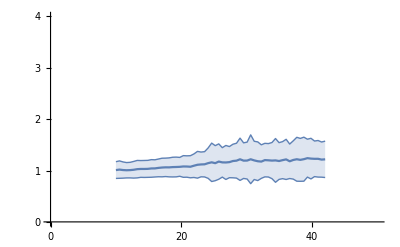

```mathematica
ListLinePlot[Around[Mean[#],StandardDeviation[#]]&/@vertexDataTS[[All,All,2,2]],
PlotRange->{{0,50},{0,4}},
IntervalMarkers->"Bands",
DataRange->{10,42},
Ticks->{Range[0,50,10],Range[0,4,1]}
]
```

#### Tension anisotropy

```mathematica
selectionBox={{20,1000},{20,680}};
```

```mathematica
vertexData=With[{t=40},Module[{vertices,verticesVecs},
vertices=First/@Position[vertex2DCoordsTS[[t]],_?(inBoxQ[#,selectionBox]&),{1},Heads->False];
verticesVecs=Select[
{#,vertexVecs[#,t]}&/@vertices,
Length[#[[2]]]==3&
];
(* Project shape director onto basis vectors *)
{toCylinder[#[[1]]],dirToTensor[#[[3,1]]{#[[2,1]].#[[3,3]],#[[2,2]].#[[3,3]]}]}&/@DeleteCases[
{vertexCoordsTS[[t,#[[1]]]],vertexLocalBasis[#[[1]],t],shapeMagPhaseDir[#[[2]]]}&/@verticesVecs,
{_,_,_Missing}
]
]
];//AbsoluteTiming
```

{3.48888,Null}

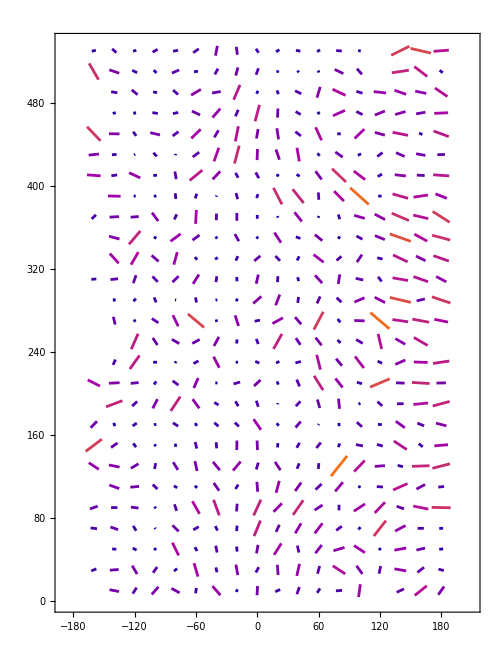

```mathematica
With[{binnedData=Mean[#[[All,2]]]&/@Select[GroupBy[vertexData,{0,-10}+Round[{0,10}+#[[1]],20]&],Length[#]>2&]},Graphics[{
AbsolutePointSize[5],AbsoluteThickness[2],
KeyValueMap[Function[{c,tensor},
With[{dir=tensorToDir[tensor]},{
Blend[{Darker@Blue,Darker@Magenta,Orange},1.5Norm[dir]],
Line[{c-20dir,c+20dir}]
}]],
binnedData
]},
ImageSize->500,Background->White,
PlotRange->{{-190,210},{0,2π $radius}},
Frame->True
]
]
```

#### LTC order parameter

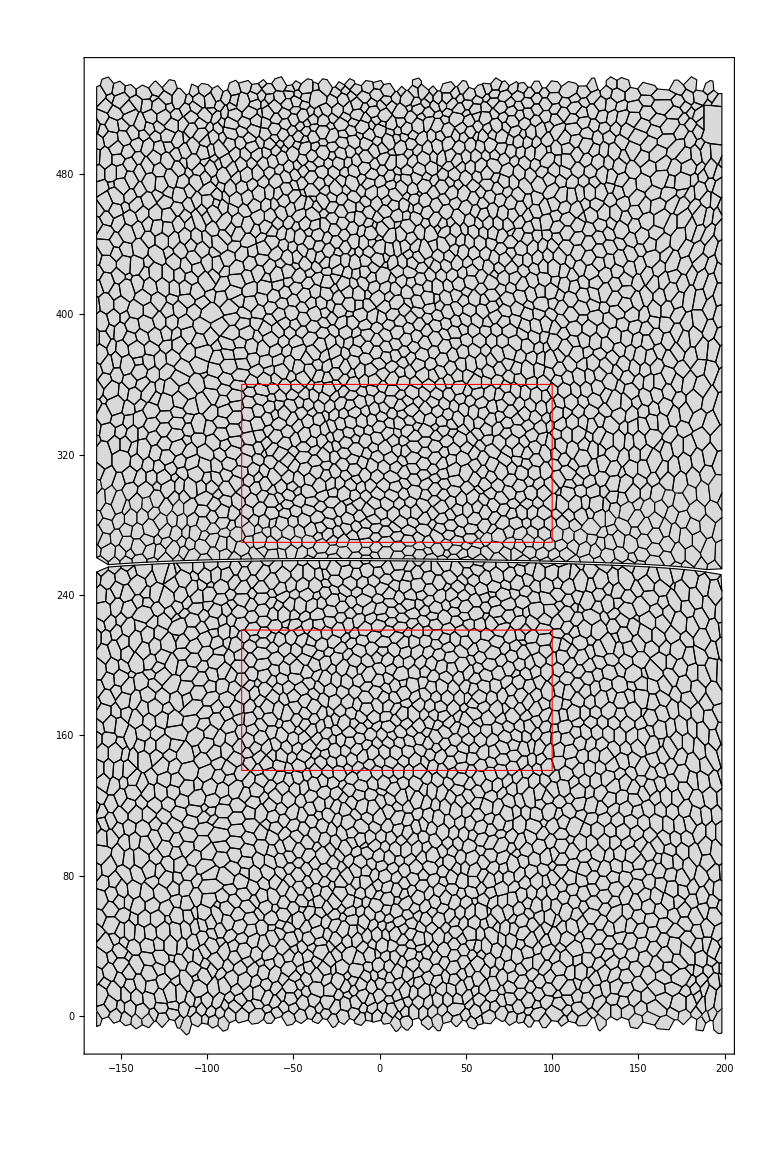

```mathematica
With[{t=10},Graphics[{
FaceForm[LightGray],EdgeForm[Black],renderCell2D[#,t]&/@Range[Length[cellCentroidsTS[[t]]]],
EdgeForm[Red],FaceForm[None],
Rectangle[{-80,270},{100,360}],
Rectangle[{-80,140},{100,220}]
},
Frame->True
]]
```

```mathematica
excludedVertices[t_]:=Union[Flatten[cellVerticesTS[[t]]/@excludedCellsTS[[t]]]]
```

```mathematica
selectedVertices=First/@Position[vertexCoordsTS[[1]],
_?(inBoxQ[toCylinder[#],{{-80,100},{270,360}}]||inBoxQ[toCylinder[#],{{-80,100},{140,220}}]&)
];
```

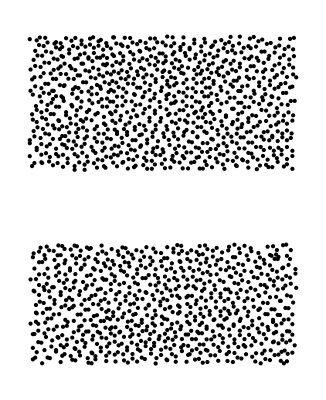

```mathematica
Graphics[Point[toCylinder[#]&/@vertexCoordsTS[[1,selectedVertices]]]]
```

```mathematica
shapeMagPhaseFromAngles[angles:{_,_,_}]:=With[{
α=π-angles[[1]],
β=π-angles[[2]],
γ=π-angles[[3]]
},
If[Total[angles]<2π-0.001,Return[{-1.0,0.0}]];
{
Sqrt[-(2 (-3+Cos[2 α]-Cos[4 α]+Cos[2 (α-β)]+Cos[2 β]-Cos[4 β]+Cos[2 (2 α+β)]+Cos[2 (α+2 β)]+Cos[2 γ]-Cos[4 γ]))/((-3+Cos[2 α]+Cos[2 β]+Cos[2 γ])^2+$MachineEpsilon)],
Abs[Mod[3(π+arcTan[Cos[2 α]-Cos[α] Cos[α+2 β],-√3 Sin[α] Sin[α+2 β]]),2π]-π]
}
];
```

```mathematica
shapeStatsTS=Block[{selectedVertices},
Table[
selectedVertices=Complement[First/@Position[vertexCoordsTS[[t]],
_?(inBoxQ[toCylinder[#],{{-80,100},{270,360}}]||inBoxQ[toCylinder[#],{{-80,100},{140,220}}]&)
],excludedVertices[t]];
Cases[shapeMagPhaseFromAngles[vertexAngles[#,t]]&/@selectedVertices,{_?(0<=#<=1&),_?(0<=#<=π&)}],
{t,Length[vertexCoordsTS]}
]];//AbsoluteTiming
```

{48.7166,Null}

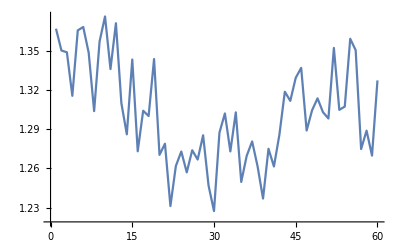

```mathematica
ListLinePlot[Mean/@shapeStatsTS[[All,All,2]]]
```

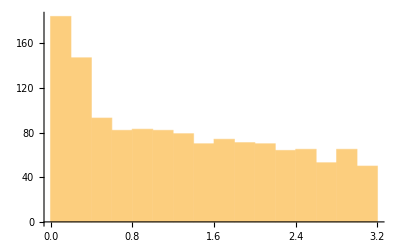

```mathematica
Histogram[shapeStatsTS[[50,All,2]]]
```

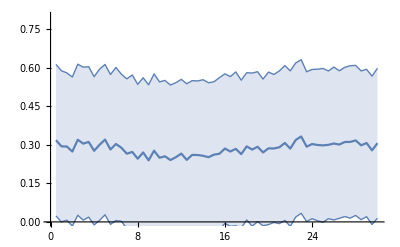

```mathematica
ListLinePlot[
Transpose[{1/2Range[Length[shapeStatsTS]],
Function[{qψ},(1/π Around[Median[#],StandardDeviation[#]]&@WeightedData[qψ[[All,2]],qψ[[All,1]]])]/@shapeStatsTS
}],
IntervalMarkers->"Bands",PlotRange->{0,0.8}
]
```